```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/src_mathematica/Ganesh

```mathematica
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
δδ[r_]:=Exp[- λ r^2];
m=938.92;mh2=m/(197.327)^2; hc=197.3269631;
Vα0[α0_,r_] :=α0  δδ[r];
```

```mathematica
Scatt1[α0_?NumberQ,rmax_?NumberQ]:=Block[{f,w},
c0=α0;
f=Replace[w,NDSolve[{w'[r]+w[r]^2-mh2 Vα0[α0,r]==0,w[0]==10^17},w,{r,0,rmax}]⟦1,1⟧];rmax-f[rmax]^-1]
Scatt2[α0_?NumberQ]:=(*JPhysB:AMO 36,4055(2003),3.1*)Block[{f,θ},f=Replace[θ,NDSolve[{θ'[ϕ]==m Sec[ϕ]^4 Sin[θ[ϕ]-ϕ]^2  Vα0[α0,Tan[ϕ]],θ[0]==0},θ,{ϕ,0,π/2},AccuracyGoal->40]⟦1,1⟧];Tan[f[π/2]]]
```

λ    a_2   C0

NDSolve::ndsz: At r == 5.04186, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {6} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 5.04186, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {6} lies outside the range of data in the interpolating function. Extrapolation will be used.

NDSolve::ndsz: At r == 5.04186, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {6} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {-965.894}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {-1080.5}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {x} = {-1194.05}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

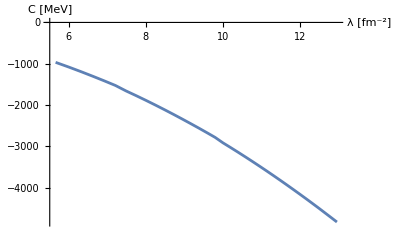

```mathematica
(*m=1;mh2=1; hc=1;*)
R=6;
(*anlo=1.;*)
anlo={0.5,5.0,10}[[2]];
(*anlo(3S1)=5.441 fm = 0.0275735 MeV^-1;*)
(*anlo(1S0)=-23.748 = -0.120348 MeV^-1;*)
Λl=Range[8,42,1.0];
aleph =anlo^-1;
LEC0s={};
res={};
ratio={};
Print["λ    a_2   C0"]
Do[{λ=Λl⟦j⟧;
C0=x/.FindRoot[Scatt1[x,R]^-1==aleph,{x,-0.1}];
AppendTo[LEC0s,    { StringPadRight[ToString[Λl⟦j⟧],6],StringPadRight[ToString[C0],12]}];
AppendTo[res,{2 √λ,C0}];
(*Print[StringPadRight[ToString[λ],5]<>"  "<>StringPadRight[ToString[aleph^-1],7]<>"  "<>StringPadRight[ToString[C0],7] ];*)
},{j,Length[Λl]}];
list=ExportString[LEC0s,"Table"];
DeleteFile["./PlotLECs.dat"];
WriteString["./PlotLECs.dat",list];
Close["./PlotLECs.dat"];
ListPlot[res,Joined->True,AxesLabel->{"λ [fm^-2]","C [MeV]"}]
```